## Model Setup

```mathematica
wm = ResourceFunction["WolframModel"];
plot = ResourceFunction["WolframModelPlot"];
randomRule = ResourceFunction["RandomWolframModel"];
```

```mathematica
randomSignature[maxRelations_, maxElements_, maxPieces_] := 
	Rule @@ Table[
		Table[
			{RandomInteger[{1, maxRelations}], RandomInteger[{1, maxElements}]},
			RandomInteger[{1, maxPieces}]
		], 
		2
	]
```

```mathematica
steps=10;
maxValue = 3;
maxVertices=3;
```

```mathematica
signature={{2,2}}->{{4,2}};
rule = {{{1,2},{1,3}}->{{1,4},{4,5},{5,2},{3,5}}};
```

URLRead::invhttp: Could not resolve host: www.wolframcloud.com.

URLFetch::invhttp: A library error occurred. The raw details are: "libcurl error (6): Could not resolve host: pacletserver.wolfram.com"

PacletInstall::dwnld: An error occurred downloading paclet Wolfram__LLMFunctions-1.7.0 from site https://pacletserver.wolfram.com: Could not reach server..

General::ChatbookInternal: An unexpected error occurred. Report this issue »

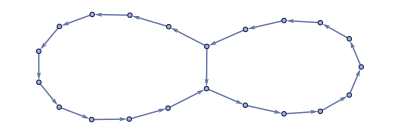

```mathematica
wm[rule, Automatic, steps, "FinalStatePlot"]
```

## Mutations

I hate this code
I want it to all use graph properties and stuff
but it’s a huge pain to extract the right parts of the rule as graphs
and also trying to operate on graphs is fucked because apparently they’re atomic expressions which is rly cool
maybe i just don’t know how to do it but whatever i guess this works
possibly there will be small issues like adding vertices that don’t make sense (e.g. vertices 1-5 +7) that will snowball out of control
but fk it we ball

also note that these all operate on rules as lists of replacements
currently they can (theoretically, untested) operate on rules with arbitrary numbers of replacements
next steps would include being able to add new full replacements rules, and remove them (possibly randomly, possibly just by allowing for deletion of the last edge in a list (? i guess you could delete the last one in a right side without anything being bad but not the left side))

```mathematica
maxElement[rule_] := Max[Flatten[List @@@ rule]]
```

```mathematica
addRandomElement[rule_] :=
	Module[{pos, edge, elem, maxElem},
		pos = RandomChoice[Position[rule, _, {3}, Heads -> False]];
		edge = Extract[rule, pos];
		elem = RandomChoice[edge];
		maxElem = maxElement[rule];
			ReplacePart[rule, pos -> Append[edge, RandomInteger[{1, maxElem+1}]]]
	]
```

```mathematica
(* remove random vertex from a random hyperedge with more than two elements *)
(* if no such hyperedges are present, return unmodified rule *)
removeRandomElement[rule_]:=
	Module[{pos, edge, newEdge, positions},
			positions = Select[Position[rule, _, {3}, Heads -> False],
					Length[Extract[rule, #]] > 2 &];
			If[positions == {},
				rule,
				CompoundExpression[
					pos = RandomChoice[positions];
					edge = Extract[rule, pos],
					newEdge = Delete[edge, RandomInteger[{1, Length[edge]}]],
					ReplacePart[rule, pos -> newEdge]
				]
			]
		]
```

```mathematica
replaceRandomElement[rule_] :=
	Module[{pos, elem, maxElem, choices},
		pos = RandomChoice[Position[rule, _, {4}, Heads -> False]];
		elem = Extract[rule, pos];
		maxElem = maxElement[rule];
		choices = If[maxElem > 1, Delete[Range[1, maxElem], elem], {1}];
		ReplacePart[rule, pos -> RandomChoice[choices]]
	]
```

```mathematica
rule
```

{{{1,2,3},{3,2,4}}→{{5,4,6},{7,4,8},{9,6,10},{11,10,2}}}

URLRead::invhttp: Could not resolve host: www.wolframcloud.com.

URLFetch::invhttp: A library error occurred. The raw details are: "libcurl error (6): Could not resolve host: pacletserver.wolfram.com"

PacletInstall::dwnld: An error occurred downloading paclet Wolfram__LLMFunctions-1.7.0 from site https://pacletserver.wolfram.com: Could not reach server..

General::ChatbookInternal: An unexpected error occurred. Report this issue »

```mathematica
replaceRandomElement[rule]
```

{{{1,2,3},{3,2,4}}→{{5,4,6},{7,4,11},{9,6,10},{11,10,2}}}

URLExecute::invhttp: A library error occurred. The raw details are: "libcurl error (6): Could not resolve host: www.wolframcloud.com"

URLRead::invhttp: Could not resolve host: www.wolframcloud.com.

URLFetch::invhttp: A library error occurred. The raw details are: "libcurl error (6): Could not resolve host: pacletserver.wolfram.com"

PacletInstall::dwnld: An error occurred downloading paclet Wolfram__LLMFunctions-1.7.0 from site https://pacletserver.wolfram.com: Could not reach server..

URLFetch::invhttp: A library error occurred. The raw details are: "libcurl error (6): Could not resolve host: pacletserver.wolfram.com"

PacletInstall::dwnld: An error occurred downloading paclet Wolfram__LLMFunctions-1.7.0 from site https://pacletserver.wolfram.com: Could not reach server..

General::ChatbookInternal: An unexpected error occurred. Report this issue »

```mathematica
addRandomEdge[rule_]:=
	Module[{pos, edges, newEdge, maxElem},
		pos = RandomChoice[Position[rule, _, {2}, Heads -> False]];
		edges = Extract[rule, pos];
		maxElem = maxElement[rule];
		newEdge = Table[RandomInteger[{1, maxElem}], 2];
		ReplacePart[rule, pos -> Append[edges, newEdge]]
	]
```

```mathematica
removeRandomEdge[rule_]:=
	Module[{pos, positions, edge, edges},
		positions = Select[Position[rule, _, {2}, Heads -> False],
				Length[Extract[rule, #]] > 1 &
			];
		If[positions == {},
			rule,
			CompoundExpression[
				pos = RandomChoice[positions],
				edges = Extract[rule, pos],
				edge = RandomInteger[{1, Length[edges]}],
				ReplacePart[rule, pos -> Delete[edges, edge]]
			]
		]
	]
```

## Evolution

```mathematica
evolveRule[startRule_, fitnessFunction_, nGenerations_, maxTries_:10] :=
	Block[{rule, fitness, newRule, newFitness},
		NestList[CompoundExpression[
			Do[
				newRule = replaceRandomElement[First[#]];
				newFitness = fitnessFunction[newRule];
				If[newFitness >= Last[#], rule=newRule; fitness=newFitness; Break],
			maxTries
			],
			{rule, fitness}
		]&,
		{startRule, fitnessFunction[startRule]},
		nGenerations]
]
```

## Fitness Functions

```mathematica
ruleDimension[rule_, nSteps_] := graphDimension[Graph[Sow[wm[rule, Automatic, nSteps, "FinalState"]]]]
```

```mathematica
graphDimension[graph_] :=
	If[ConnectedGraphQ[graph],
		ResourceFunction["WolframHausdorffDimension"][graph, All, "AllDimensions", "VertexMethod" -> Max],
	0] // If[NumberQ[#], #, 0]&
```

```mathematica
nearnessTo3D[rule_] := -Abs[ruleDimension[rule, 7] -3]
```

```mathematica
(* average ratio between numbers of vertices on successive steps *)
(* 0 for non-connected final graphs *)
vertexGrowthRate[rule_] :=
	With[{evolution = wm[rule, Automatic, 7]},
		If[ConnectedGraphQ[Graph[evolution["FinalState"]]],
		N[Mean[
			Ratios[
			evolution["VertexCountList"] //
				Function[nVertices, PadRight[nVertices, 6, Last@nVertices]]
		]]],
	0]
]
```

```mathematica
edgeGrowthRate[rule_] :=
	With[{evolution = wm[rule, Automatic, 7]},
		If[ConnectedGraphQ[evolution["FinalState"]],
			N[Mean[Ratios[
				evolution["EdgeCountList"] //
					Function[nEdges, PadRight[nEdges, 6, Last@nEdges]]
		]]],
	0]
]
```

## Compare Evolutions

```mathematica
graphRule[rule_, steps_:7] := wm[rule, Automatic, steps, "FinalStatePlot"]
```

```mathematica
compareEvolutions[evolutions_] :=
	Column[Function[evolution, Row[Labeled[graphRule[First[#]], Last[#]]&/@evolution]]/@ evolutions]
```

```mathematica
evolutions = ParallelMap[Function[rule, evolveRule[rule, Function[r, -Abs[ruleDimension[r, 7]-3]], 5]] , Table[rule, 5]];
```

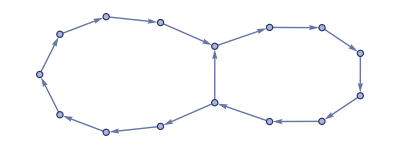
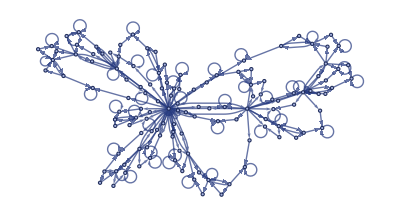
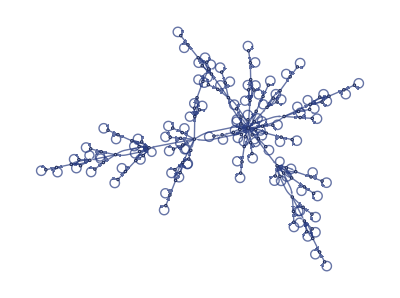
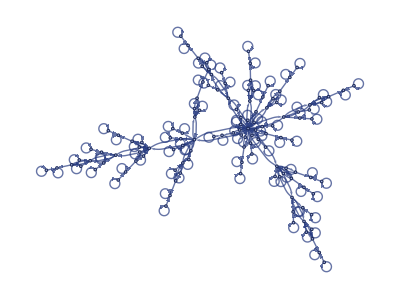
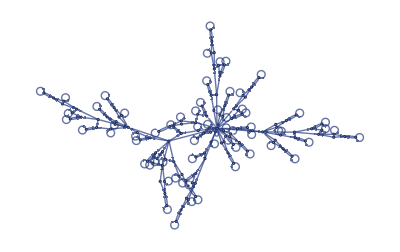
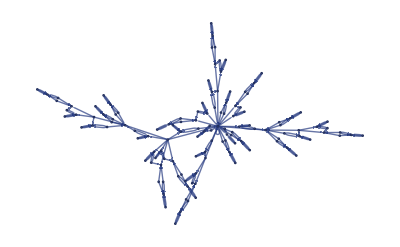
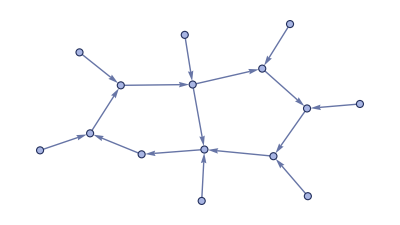
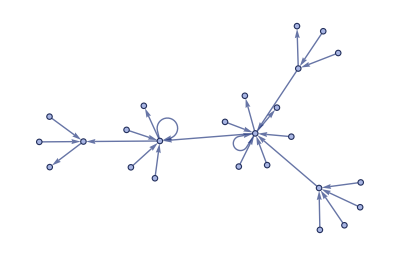
-Graphics--1.3555-Graphics--0.0897133-Graphics--0.0846-Graphics--0.0846-Graphics--0.0110531-Graphics--0.0110531
-Graphics--1.3555-Graphics--0.898989-Graphics--0.429971-Graphics--0.072393-Graphics--0.000836282-Graphics--0.000836282
-Graphics--1.3555-Graphics--0.170925-Graphics--0.0846745-Graphics--0.0846745-Graphics--0.0846745-Graphics--0.0846
-Graphics--1.3555-Graphics--1.02099-Graphics--0.308736-Graphics--0.308736-Graphics--0.241025-Graphics--0.170951
-Graphics--1.3555-Graphics--1.-Graphics--1.-Graphics--1.-Graphics--1.-Graphics--0.678072

```mathematica
compareEvolutions[evolutions]
```

```mathematica
ListLinePlot[Function[evo,Callout[Last[#], graphRule[First[#]]]&/@evo]/@evolutions]
```

-Graphics-

## Animate evolution of single rule

```mathematica
coolRule={{{1,2},{5,3}}->{{1,4},{4,2},{5,4},{3,4}}}
```

{{{1,2},{5,3}}→{{1,4},{4,2},{5,4},{3,4}}}

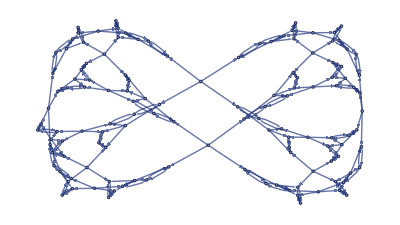

```mathematica
graphRule[coolRule]
```

```mathematica
ruleEvo = wm[coolRule, Automatic, 8, "StatesList"];
```

```mathematica
ListAnimate[Graph/@ruleEvo]
```

## TODO

#### Issues

#### New fitness functions

Rules whose dimensions stabilize

Different dimension estimates

Edge to vertex ratios

Measure of repetition / complexity

#### Utilities

Show change in rules across evolution

Plot in rule space

#### Rule Mutations

Add and remove vertices

Add and remove edges

Add and remove replacements

Crossover

#### Replication of Wolfram study for Genetic CA Evolution

Sequences of random single point mutations

Show sequences of mutations in rule

Show sequence of produced phenotypes

Render path in dimension-reduced rule space (how?)

Develop multiway graphs for sequences of rule mutations

Build fitness-neutral sets (set of rules with same fitness along with mutation relationships between them

Try out different ways to visualize fitness landscape of possible mutations

Key question: how well can adaptive evolution maximize different kinds of objectives?

## Exhaustive Rule Analysis

```mathematica
signature = {{2,2}}->{{3,2}};
```

```mathematica
allRules = ResourceFunction["EnumerateWolframModelRules"][signature];
```

ResourceFunction::usermessage: ParallelMapMonitored

```mathematica
ruleDimensions=Association@@ParallelMap[#->ruleDimension[#, 7]&, allRules] // Sort;
```

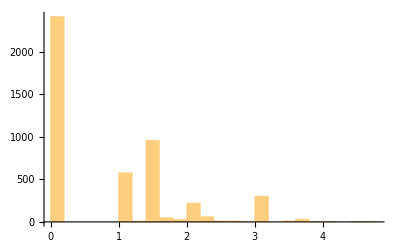

```mathematica
Histogram[Values[ruleDimensions]]
```

```mathematica
maxRule=Last[Keys[ruleDimensions]]
```

{{1,2},{3,2}}→{{1,2},{3,2},{4,2}}

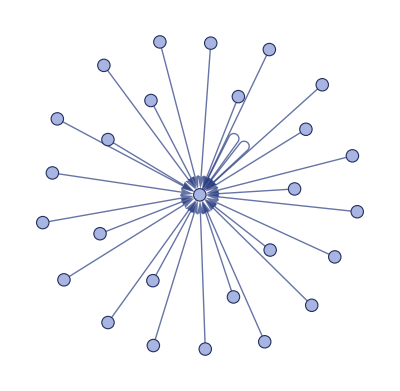

```mathematica
wm[maxRule, {{1,1},{1,1}}, 7, "FinalStatePlot"]
```

## Multiway graph of rule changes

Make every possible replacement for a rule

Go down to lowest level

Table of rules for replacement of each element from 1 to max element

Make all replacements that improve fitness

Make every possible replacement

Test all for fitness and keep increased (and same) fitness rules

Create edges from rule to improved / modified rule

Option A: Use NestList and apply evolution function to right side of previous edges

Option B: Evolve and Sow lists of all improved rules then build graph with Reap afterwards

```mathematica
allReplacements[rule_]:=
Function[pos, Map[ReplacePart[rule, pos->#]&,Delete[Range[1, maxElement[rule]+1], Extract[rule, pos]]]]/@Position[rule, _, {4}, Heads->False]//Flatten
```

```mathematica
rule = {{{1,1}}->{{1,1}}};
allReplacements[rule]//Column
```

{{2,1}}→{{1,1}}
{{1,2}}→{{1,1}}
{{1,1}}→{{2,1}}
{{1,1}}→{{1,2}}

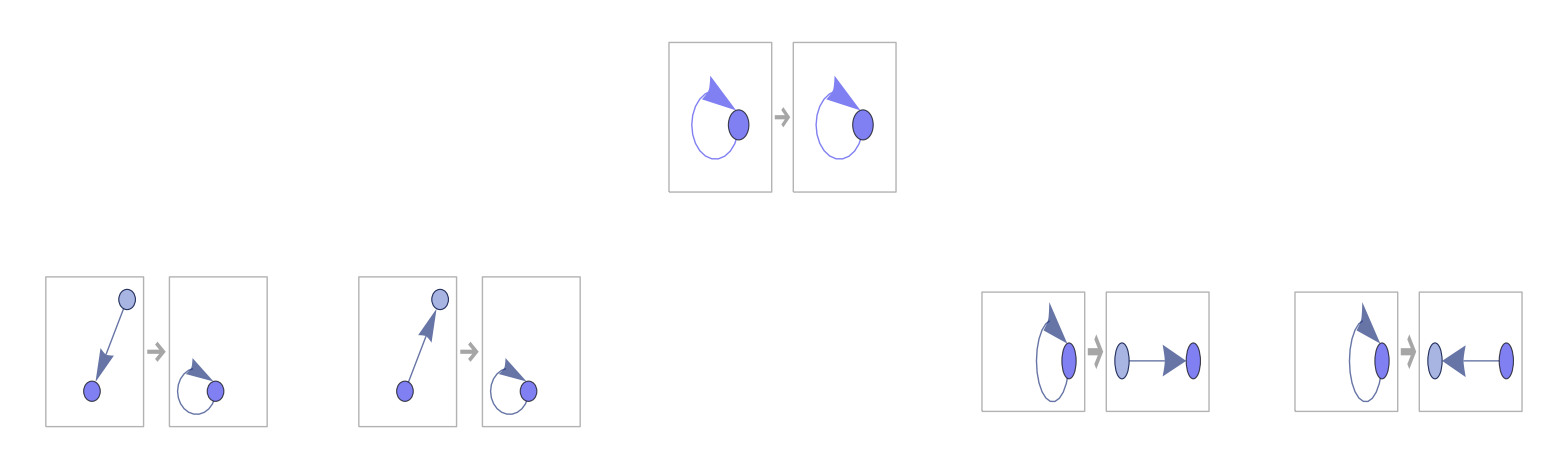

```mathematica
Graph[rule->#&/@allReplacements[rule], VertexShapeFunction:>(Inset[showRule[#2],#1, Center, 0.6]&),ImagePadding->40]
```

```mathematica
allRules = ResourceFunction["EnumerateWolframModelRules"][{{1,2}}->{{1,2}}]
```

OptionValue::nodef: Unknown option ProgressReporting for ParallelMap.

{{{1,1}}→{{1,1}},{{1,1}}→{{1,2}},{{1,1}}→{{2,1}},{{1,2}}→{{1,1}},{{1,2}}→{{1,2}},{{1,2}}→{{2,1}},{{1,2}}→{{2,2}},{{1,2}}→{{1,3}},{{1,2}}→{{2,3}},{{1,2}}→{{3,1}},{{1,2}}→{{3,2}}}

## Evolve full generations with stochastic selection

```mathematica
evolveGenerations[initialPop_, fitnessFunction_, nGenerations_]:=
Module[{currentGen, nextGen, mutations, fitnesses},
Nest[Function[currentGen,
CompoundExpression[
mutations=replaceRandomElement/@currentGen,
Sow[MapThread[Rule, {currentGen, mutations}], "mutations"],
nextGen=Join[initialPop, mutations],
fitnesses = fitnessFunction/@nextGen,
Sow[AssociationThread[nextGen, fitnesses], "fitness"],
Sow[RandomSample[fitnesses->nextGen, Length[initialPop]], "generations"]
]],
initialPop, nGenerations
]]
```

LLMFunctions::llmrstrt: New updates have been installed. Restart the Wolfram system to apply the changes.

```mathematica
signature={{2,2}}->{{4,2}};
initialRule = {randomRule[signature]};
initialPop = Table[replaceRandomElement[initialRule], 5];
```

```mathematica
(*initialPop = Table[{randomRule[signature]},5];*)
nGenerations=5;
fitnessFunction=(nearnessTo3D[#]+3.1)&;
```

```mathematica
{lastGen, {mutations, fitnesses, generations}}=Reap[evolveGenerations[initialPop, fitnessFunction, nGenerations], {"mutations", "fitness", "generations"}];
```

```mathematica
mutations=Flatten[mutations, 1];
generations = Flatten[generations, 1];
```

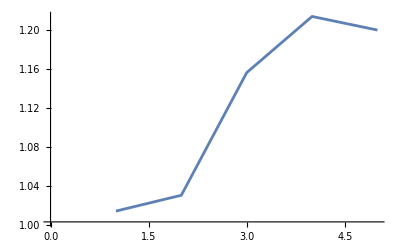

```mathematica
(* mean fitness by generation *)
ListLinePlot[Mean/@Flatten[Values/@fitnesses,1]]
```

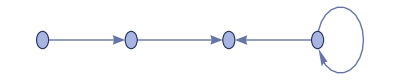
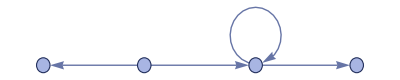
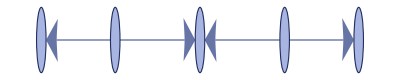
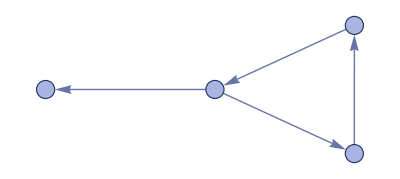
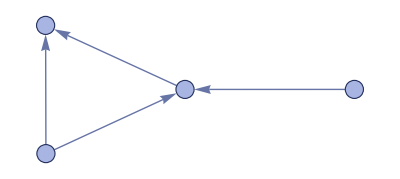
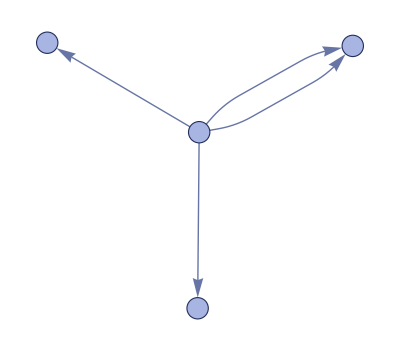
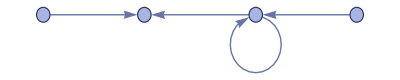
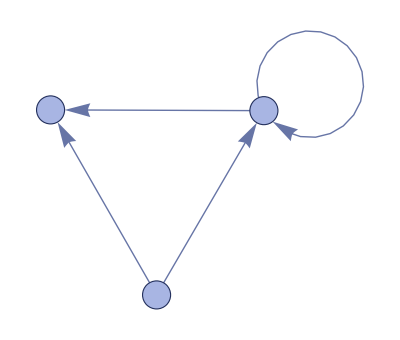
-Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
(* chosen phenotypes by generation *)
Column[
Map[Function[generation, Row[graphRule/@generation]], generations]]
```

```mathematica
initialMutations = Rule[initialRule, #]&/@initialPop;
```

```mathematica
allMutations=Join[initialMutations, Catenate[mutations]];
```

```mathematica
vfGraph[{x_,y_},r_,{w_,h_}]:=Inset[graphRule[r], {x,y}]
```

```mathematica
vfRule[{x_,y_},r_,{w_,h_}]:=Inset[RulePlot[wm[r]], {x,y}, Automatic,{w,h}]
```

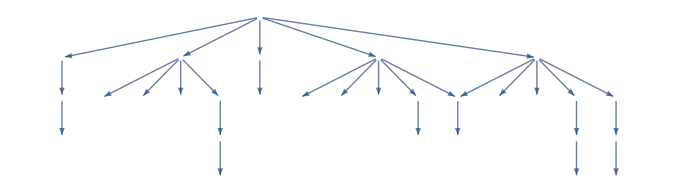
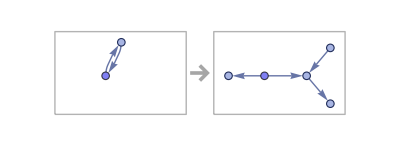
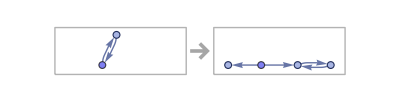
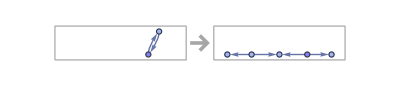
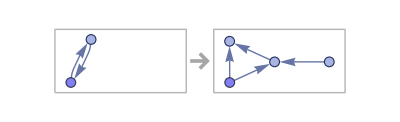
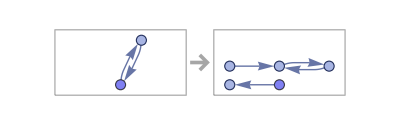
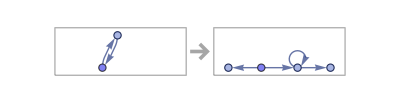
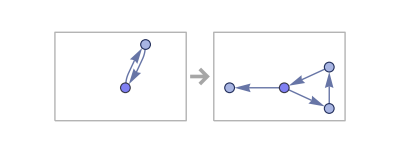

```mathematica
Graph[allMutations,
GraphLayout->{"LayeredDigraphEmbedding","RootVertex"->initialRule},
VertexShapeFunction->vfRule
]
```